-Graphics-

# Introduction To Neural Networks

## Tuseeta Banerjee Research Scientist, Machine Learning

-Graphics-

-Graphics-

## Why use Neural Networks?

“It [AI] would take off on its own and redesign itself at an ever increasing rate. Humans, who are limited by slow biological evolution, couldn’t compete and would be superseded.” - Stephen Hawking

-Graphics-

If you haven’t used “machine learning,” “deep learning” and “neural networks” yourself, you’ve almost certainly heard of them. They’re everywhere. You may be familiar with their commercial use in self-driving cars, image recognition, automatic text completion, text translation and other complex data analysis, but you can also train your own neural nets to accomplish tasks like identifying objects in images, generate sequences of text, or segment pixels of an image. With the Wolfram Language, you can get started with machine learning and neural nets faster than you think. Since deep learning, AKA neural networks are everywhere, let’s go ahead and explore what exactly they are and how you can start using them.

### Image classification

```mathematica
net=NetModel["Inception V3 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
image=-Graphics-;
```

```mathematica
net[image]
```

Labrador retriever

## Learning Objectives

### Network Data

Neural networks internally represent information as numeric tensors. So first we need to understand how to convert different data types to tensors.

Tensors

Encoders and Decoders

### Network Structure

Complicated neural networks are built up from a few foundational data types. To understand more advanced networks, we must first familiarize ourselves with the basic constructs, including

Layers

Network Constructors

### Network Training

Given a neural network, we see how we can train these networks in an optimized fashion:

Basic theory of training

Loss Layers

Improving various methods

Initializing Weights

### Regression Examples

Basic Regression

Regression on Vectorized Data

Options in NetTrain

## What are Neural Networks?

Neural networks are a programming approach that is inspired from the neurons in the human brain, and enables computers to learn from observational data: be it images, audio, text, labels, strings or numbers. They try to model some unknown function (for example,  f: P → Q) that maps this data into numbers or classes, by recognizing patterns in the data. They are built from these components:

Encoders and Decoders (to convert the input data type to numeric tensors)

Layers (to perform operations on these tensors depending on the applications)

Containers (to hold these operations in a sensible way)

Once the neural network is build from the above three components, it needs to be trained (in other words, optimized). In Wolfram Language, Neural Networks are build on the following paradigm:

-Graphics-

As you might have guessed, the optimization (or minimizing the “loss” of the network) is done through stochastic gradient descent in an iterative fashion. The inputs are fed to the net repeatedly, the error/loss is computed each time, then used to update the model’s parameters using back propagation. Back Propagation, or “Back Error Propagation” involves distributing the error computed during forward propagation back to the network’s layers.

## Network Data: Tensors

### Ranks of tensors

Tensors are multidimensional arrays.

Rank 0 (scalars): 0.0

Rank 1 (vectors): {0.0, 1.0}

Rank 2 (matrices): {{1.,2.,3.} , {3., 2., 1.}}

Rank n tensors: {... {... {1., 2., 3.}...}...}

### Examples of Tensors

Vectors as coordinates of points

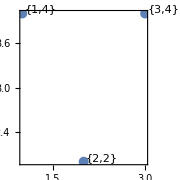
-Graphics-  ≈ ( | 1 |  | 4 | )
( | 3 |  | 4 | )
( | 2 |  | 2 | )

```mathematica
data={{1,4},{3,4},{2,2}};
plot=ListPlot[Labeled[#,Framed[#,FrameStyle->None]]&/@data,Frame->True,LabelStyle->Medium,AspectRatio->1,PlotRangePadding->1,PlotStyle->PointSize[0.04],ImageSize->Small];
gr=Grid[{{Style["(",20],Style[1,20],Spacer[1],Style[4,20],Style[")",20]},{Style["(",20],Style[3,20],Spacer[1],Style[4,20],Style[")",20]},{Style["(",20],Style[2,20],Spacer[1],Style[2,20],Style[")",20]}}];Row[{plot, Spacer[60], Style["  ≈ ",32], Spacer[60], gr}]
```

Matrices as Grayscale images

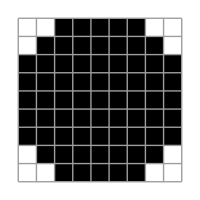
-Graphics-  ≈ (0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

```mathematica
Row[{ArrayPlot[DiskMatrix[4],Mesh->All,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60], MatrixForm@DiskMatrix[4]}]
```

Rank-3 tensors as colored image

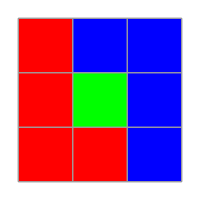
-Graphics-  ≈ ((1 | 0 | 0
1 | 0 | 0
1 | 1 | 0) | (0 | 0 | 0
0 | 1 | 0
0 | 0 | 0) | (0 | 1 | 1
0 | 0 | 1
0 | 0 | 1))

```mathematica
re={1,0,0};bl={0,0,1};gr={0,1,0};data={{re,bl,bl},{re,gr,bl},{re,re,bl}};img=Image[data];Row[{ArrayPlot[ImageData@img,ColorFunction->RGBColor,Mesh->True,ImageSize->200], Spacer[60], Style["  ≈ ",32], Spacer[60],MatrixForm[{MatrixForm/@Round[Transpose[data,{2,3,1}]]}]}]
```

## Class Encoders

NetEncoder is used to convert any data we receive to an input tensor. Similarly, after we have done the optimization (training), we convert the output tensor to the data format we started with using NetDecoder.

#### Class encoders and decoders

Encode the user defined class (here the class of male and females)

```mathematica
enc=NetEncoder[{"Class",{"male","female"}}]
```

NetEncoder[<>]

Use it to create the input tensor

```mathematica
enc[{"male","female","female"}]
```

{1,2,2}

Create the decoder for the same classes

```mathematica
dec=NetDecoder[{"Class",{"male","female"}}]
```

NetDecoder[<>]

Use probabilistic approach to decode the output (make sure each of the tensor to be decoded follows the dimension specification of the decoder)

```mathematica
dec[{{0.1,0.2},{0.9,0.7}}]
```

{female,male}

## Character Encoders

Encoding all the ASCII characters

```mathematica
enc=NetEncoder["Characters"]
```

NetEncoder[<>]

Convert “hello world” to its ASCII counterpart

```mathematica
enc["hello world"]
```

{75,72,79,79,82,3,90,82,85,79,71}

Creating a decoder for the characters

```mathematica
dec=NetDecoder["Characters"]
```

NetDecoder[<>]

Decoding the sentence by converting it to the vector representation in complete ASCII basis

```mathematica
codes={75,72,79,79,82,3,90,82,85,79,71};
matrix=UnitVector[97,#]&/@codes;
matrix[[1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The encoder converts the data to a number. Please note that the decoder has dimensions of the number of class labels in the encoder. In the ASCII character example,  the dimensions. (or how to convert a word to a vector of length of the Character codes we have) of the matrix shows that the character to decode has the same length as the count in the decoder.

Making sure that each character to decode has the same length as the count in the decoder, by checking the Dimensions input matrix

```mathematica
Dimensions[matrix]
```

{11,97}

```mathematica
dec[matrix]
```

hello world

## Image Encoders

#### Image encoder

```mathematica
image= -Graphics-;
```

```mathematica
enc=NetEncoder[{"Image",ImageDimensions[image],ColorSpace->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
encoded=enc[image];
```

```mathematica
dec=NetDecoder[{"Image",ColorSpace->"Grayscale"}]
```

NetDecoder[<>]

```mathematica
dec[encoded]
```

-Graphics-

## Layers

A neural network is a biologically inspired model and consists of “layers” or “neurons” through which information is processed from the input to the output tensor. Layers are usually defined by their mathematical operation

The figure below shows a simple construction of a feed-forward Neural Network

Source:http://cs231n.github.io/neural-networks-1/

The implemented layers in the Wolfram Language are:

```mathematica
{{"Layer Type", "Layers"}, {"Basic Layers ", LinearLayer | ElementwiseLayer | SoftmaxLayer}, {"Elementwise Computation Layers", ElementwiseLayer | ThreadingLayer  | ConstantTimesLayer  | ConstantPlusPlayer}, {"Convolution and Filtering Layers", ConvolutionLayer | DeconvolutionLayer | PoolingLayer | ResizeLayer |  SpecialTransformationLayer}, {"Training Optimization Layers", ImageAugmentationLayer | NormalizationLayer | DropoutLayer | LocalResponseNormalizationLayer | InstanceNormalizationLayer}, {"Structure Manipulation Layers", CatenateLayer | FlattenLayer | ReshapeLayer | ReplicateLayer |  PaddingLayer | PartLayer | TransposeLayer| AppendLayer | PrependLayer|ExtractLayer}, {"Array Operation Layers", ConstantArrayLayer | SummationLayer | TotalLayer | AggregationLayer | DotLayer|OrderingLayer}, {"Recurrent Layers", BasicRecurrentLayer |  GatedRecurrentLayer | LongShortTermMemoryLayer}, {"Sequence-Handling Layers", EmbeddingLayer | SequenceLastLayer | SequenceReverseLayer | SequenceMostLayer | SequenceRestLayer | AttentionLayer | UnitVectorLayer}}
```

## Now what?

Generally, most people use the following rule of thumb:

-Graphics-

So, it makes us wonder: how do you stack them? The answer leads us to the third component we mentioned.

## Stacking Layers: NetChain

NetChain can be used to connect different layers in a chain like fashion to create a neural net.

#### A single layer chain:

```mathematica
net=NetChain[{ElementwiseLayer[Tanh]}]
```

NetChain[<>]

```mathematica
net[{-1,0,1}]
```

{-0.761594,0.,0.761594}

This is simply applying the Tanh function to the data

```mathematica
Tanh[{-1,0,1}]//N
```

{-0.761594,0.,0.761594}

#### Use special syntax for linear and elementwise layers

```mathematica
NetChain[{3,Tanh,4,Ramp,5}]
```

NetChain[<>]

## Stacking Layers: NetGraph

NetGraph can be used to connect different layers to create graphical neural network of any topology.

#### Constructing a chain using NetGraph

```mathematica
net=NetGraph[{2,Ramp,4,Ramp,8},{1->2->3->4->5}]
```

NetGraph[<>]

This is equivalent to a NetChain

```mathematica
NetChain[{2,Ramp,4,Ramp,8}]
```

NetChain[<>]

#### Combining two layers

```mathematica
net=NetGraph[{Ramp,Tanh,Times,Plus},{1->2->3,1->3->4,2->4}]
```

NetGraph[<>]

```mathematica
data={-2,-1,0,1,2}
```

{-2,-1,0,1,2}

```mathematica
net[data]
```

{0.,0.,0.,1.52319,2.89208}

The seemingly complicated network structure is actually doing the following operation:

```mathematica
Tanh@Ramp@data*Ramp@data+Tanh@Ramp@data//N
```

{0.,0.,0.,1.52319,2.89208}

#### Concatenating output from intermediate layers

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,CatenateLayer[]},{1->2,{1,2}->3}]
```

NetGraph[<>]

#### NetChain can be used as a part of a NetGraph

```mathematica
chain=NetChain[{ElementwiseLayer[Ramp],ElementwiseLayer[LogisticSigmoid]}]
```

NetChain[<>]

```mathematica
NetGraph[{BatchNormalizationLayer[],chain},{1-> 2}]
```

NetGraph[<>]

## Stacking Layers: NetPort

NetPort represents the specified port for a layer in a NetGraph or similar structure.

### Creating a simple total NetGraph with two inputs

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid,TotalLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->2,{1,2}->3}]
```

NetGraph[<>]

### Creating a net with two outputs

```mathematica
net=NetGraph[{Ramp,LogisticSigmoid},{1->2,1->NetPort["Output1"],2->NetPort["Output2"]}]
```

NetGraph[<>]

### Creating a net which explicitly computes a loss

In this example the “shape” of the NetPort is determined by specifying the Input to Scalar

```mathematica
net=NetGraph[{ElementwiseLayer[Tanh],DropoutLayer[],MeanSquaredLossLayer[]},{1->NetPort[3,"Target"],2->NetPort[3,"Input"]}]
```

NetGraph[<>]

## Network Training: Basic Theory

### Neural Networks Learn on Training Data

Neural networks are data-driven algorithms.

You can think of training data as implicitly specifying a function, where training “tunes” a net to approximate this function.

### Basic Theory

Training a network finds a (local) optimum of the loss as a function of the learned parameters

To train one parameter x, the error or cost function or loss ϵ of the network is computed on the entire training data. The chain rule is used to back-propagate the error ϵ through the network. (Full Batch Gradient Descent)

Updating the parameter x→x- lr ∂x is known as gradient descent with learning rate lr. Here is an example which shows how the error (cost function) is minimized with respect to the two parameters, using Gradient Descent.

```mathematica
f[x_,y_]:=x^4-2x^2+2y^4-2y^2+2x y 
pts = Reap[FindMinimum[x^4-2x^2+2y^4-2y^2+2x y ,{{x,-2.0},{y,-2.0}},Method-> "ConjugateGradient",StepMonitor:>Sow[{x,y}]]][[2,1]];
pts =Join[{{-2.0,-2.0}},pts];
table=Table[{pts[[i,1]],pts[[i,2]],f[pts[[i,1]],pts[[i,2]]]},{i,1,Length[pts]}];
Show[Plot3D[f[x,y],{x,-2,2.0},{y,-2,2.0},MeshFunctions->{#3&},Mesh->50, ColorFunction->"BeachColors"],Graphics3D[{Black,Thick,Line[table]}],Graphics3D[{PointSize[Large],Red,Point[table]}]]
```

-Graphics3D-

However, when the data is repetitive or too large it is often more useful to train one parameter x, the error or loss or cost function ϵ of the network is computed on the subsets(or batches) training data (Mini-batch Gradient Descent/ Stochastic Gradient Descent)

The parameters of the network gradually converge on a local optimum, i.e. the error is minimized.

In practice, more complicated update schemes can be used by setting the Method option in NetTrain.

For training a neural network, the function NetTrain is used. NetTrain performs a lot of operations automatically: it will initialize the parameters in the layers, decide on the initial learning rate, the method for updating the parameters, the learning rate schedule, the batch size and the loss functions to use. However, you can modify the default options in NetTrain (please refer to the notes/reading materials at the end of options section of NetTrain).

## A Simple Regression Problem

### LinearLayer

A Linear Layer is an affine transformation x →  Ax + b  where A is the “weight matrix” and the vector b is the “bias vector”. This type of layer has a lot of parameters, and hence used towards the end of the network (after the dimensions of the tensor has been reduced). To understand what a Linear Layer does , it is easiest to construct a net with single LinearLayer, which is solving a simple linear approximation.

```mathematica
data={2,10,3};
layer=NetInitialize@LinearLayer[2,"Input"-> 3]
layer[data]
```

LinearLayer[<>]

{-10.6364,12.1177}

```mathematica
linear[data_, weight_,bias_]:=Dot[weight,data]+bias
```

```mathematica
linear[data,Normal@ NetExtract[layer,"Weights"],Normal@NetExtract[layer,"Biases"]]
```

{-10.6364,12.1177}

### ElementwiseLayer

The Elementwise Layer applies a unary function f to every element of the input tensor. The function f, is referred to as the activation function in literature; Common choices for this so-called ‘activation function’ are  LogisticSigmoid, Tanh, Ramp (Rectified Linear Unit, ReLU).

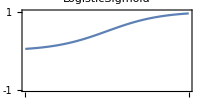
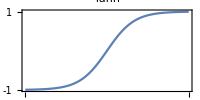
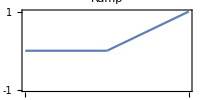

```mathematica
Row[Table[
{min,max}={-1,1}*If[f===Ramp,1,3];
Plot[f[x],{x,min,max},PlotLabel->f,ImageSize->200,Frame->True,PlotRange->{{min,max},{-1,1}},AspectRatio->0.5,FrameTicks->{{{-1,0,1},{}},{{min,0,max},{}}}],{f,{LogisticSigmoid,Tanh, Ramp}}], Spacer[50]]
```

```mathematica
elem=ElementwiseLayer[Tanh];
data=RandomReal[{0,10},10];
elem[data]
```

{0.999998,0.550406,0.971323,1.,1.,1.,0.936297,0.96712,0.0604077,1.}

As we would expect, it applies Tanh to the data

```mathematica
Tanh[data]
```

{0.999998,0.550406,0.971323,1.,1.,1.,0.936297,0.96712,0.0604077,1.}

### SoftmaxLayer

The Softmax classifier takes a vector as input and returns normalized exponential values as class probabilities. The element x_i in a vector is converted to e^x_i/∑_j e^x_j,  and generally the innermost dimension is used as the normalization dimension.

We apply the SoftmaxLayer on a list of RandomData to get probabilistic interpretations. On a list:

```mathematica
data=RandomReal[{0,10},10];
{SoftmaxLayer[]@data,Total@SoftmaxLayer[]@data}
```

{{0.489507,0.120208,0.352239,0.00101612,0.010277,0.0205173,0.00247096,0.00126575,0.0000780045,0.00242051},1.}

Let’s see what SoftmaxLayer is actually evaluating by going the functional approach:

```mathematica
fsoftmax[x_]:=N@Exp[x]/Total[Exp[x],{-1}];
{fsoftmax[data],Total@fsoftmax[data]}
```

{{0.489507,0.120208,0.352239,0.00101612,0.010277,0.0205173,0.00247096,0.00126575,0.0000780045,0.00242051},1.}

## A Simple Regression Problem

### Gaussian

Two mostly separated Gaussians are a linear classification problem:

Create an artificial dataset from two normally distributed clusters:

```mathematica
makeCluster[class_,μ_,σ_]:=RandomVariate[BinormalDistribution[{μ,μ},{σ,σ},0],1000]->class;
clusters=makeCluster@@@{{Red,1,0.5},{Green,-1,0.5}};
```

Plot the dataset:

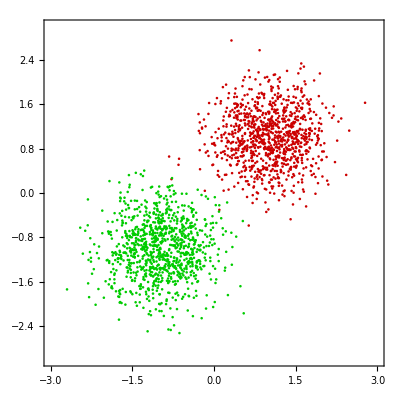

```mathematica
plot=ListPlot[Keys[clusters], PlotStyle->{RGBColor[0.8, 0., 0.],RGBColor[0., 0.8, 0.]},AspectRatio->1,Frame->True,PlotRange->{{-3,3},{-3,3}}]
```

The training data consists of rules mapping the point to the cluster it is in:

```mathematica
trainingData=Flatten[Thread/@clusters];
RandomSample[trainingData,6]
```

{{-0.637861,-1.51134}→RGBColor[0, 1, 0],{1.03116,0.794877}→RGBColor[1, 0, 0],{0.901272,1.44399}→RGBColor[1, 0, 0],{0.762479,1.37083}→RGBColor[1, 0, 0],{-0.869097,-0.205282}→RGBColor[0, 1, 0],{1.03389,1.60186}→RGBColor[1, 0, 0]}

Create a net to compute the probability of a point lying in each cluster, using a "Class" decoder to classify the input as either Red or Green

```mathematica
net=NetChain[{4 , (*First fully-connected layer*)
                          2,      (*Corresponds to 2 classes *)
                          SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green}}]]
```

NetChain[<>]

Train the net on the data:

```mathematica
trained=NetTrain[net,trainingData]
```

NetChain[<>]

Show the contours in feature space in which each class reaches a posterior probability of 0.75:

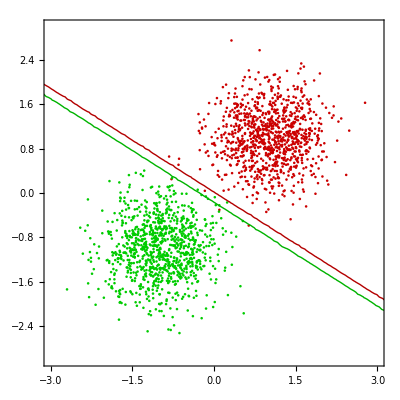

```mathematica
Show[plot,Quiet@Table[ContourPlot[trained[{x,y},{"Probability",color}]==0.75,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.3]}],{color,{Red,Green}}]]
```

### XOR

The XOR classification problem is one of the simplest examples where linear classification fails.

Create an artificial dataset for XOR classification:

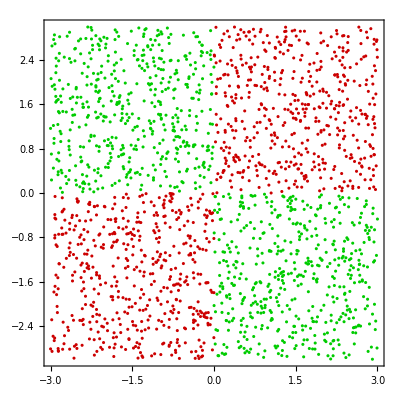

```mathematica
makeCluster[class_,r1_,r2_,r3_,r4_]:=RandomVariate[UniformDistribution[{{r1,r2}, {r3, r4}}],500]->class;
clusters=makeCluster@@@{{Red,0,3,0,3},{Red,-3,0,-3,0},{Green,-3,0,0,3},{Green,0,3,-3,0}};
plot=ListPlot[Keys[clusters], PlotStyle->{RGBColor[0.8, 0., 0.],RGBColor[0.8, 0., 0.],RGBColor[0., 0.8, 0.],RGBColor[0., 0.8, 0.]},AspectRatio->1,Frame->True,PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
trainingData=Flatten[Thread/@clusters];
net=NetChain[{10 , (*First fully-connected layer*)
                          Ramp, (*To provide the non-linearity required to draw the surfaces *)
                          2,      (*Corresponds to *)
                          SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green}}]]
```

NetChain[<>]

Training and Visualization:

NetChain[<>]

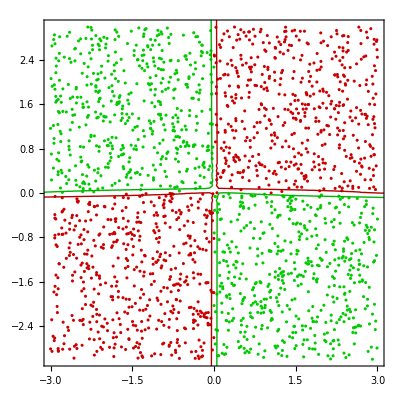

```mathematica
trained=NetTrain[net,trainingData]
Show[plot,Quiet@Table[ContourPlot[trained[{x,y},{"Probability",color}]==0.75,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.3]}],{color,{Red,Green}}]]
```

## Convolution Layers

### ConvolutionLayer

A ConvolutionLayer will apply convolution on a tensor, usually performing a downsampling/ filtering operation. It takes a kernel (square or rectangular), stride and padding to create the output. This is the core building block of Convolution Neural Networks (CNN). CNNs often have several levels of convolution layers, which pick up patterns at different levels of detail (recognize large structures, then smaller patterns etc). Conceptually, you replace the a section of pixels in an image with a weighted average of their values. The weights are the parameters of the layer.

-Graphics-

The following function computes the size of the non-channel dimensions, given the input size and parameters:

```mathematica
outputconv[inputSize_List,kernSize_,stride_,pad_,dilate_]:=Floor[(inputSize+2*pad-(dilate*(kernSize-1)+1))/stride]+1
```

The output size of an input of size {256,256}, a kernel size of {2,3}, a stride of 2, a dilation factor of {3,4}, and a padding size of {1,2}:

```mathematica
outputconv[{256,256},{2,3},2,{1,2},{3,4}]
```

{128,126}

### Deconvolution Layer

Unlike what the name suggests, a DeconvolutionLayer will not apply deconvolution operator on a tensor, but will perform an up-sampling operation. Sometimes called transposed convolution or convolution with fractional strides.

The following function computes the size of the non-channel dimensions, given the input size and parameters:

```mathematica
outputdeconv[inputSize_List,kernSize_,stride_,pad_]:=(stride*(inputSize-1)+kernSize-2*pad)
```

The output size of an input of size {256,256}, a kernel size of {2,3}, a stride of 2, a dilation factor of {3,4}, and a padding size of {1,2}:

```mathematica
outputdeconv[{256,120},3,2,2]
```

{509,237}

### Pooling Layer

A form of nonlinear downsampling, often used in CNNs in-between convolution layers. The functions that could be used are Max, Mean, Total

-Graphics-

The following function computes the size of the non-channel dimensions, given the input size and parameters:

```mathematica
outputpool[inputSize_List,kern_,stride_,pad_]:=
Floor[(inputSize+2*pad-kern)/stride]+1
```

The output size of an input of size {256,256}, a kernel size of {2,3}, a stride of 2, a dilation factor of {3,4}, and a padding size of {1,2}:

```mathematica
outputpool[{256,252},3,2,2]
```

{129,127}

## LeNet explained

LeNet is a simple convolution network that performs feature extraction that can be used to Classify images.

```mathematica
NetChain[
{

(*STEP 1: FETAURE EXTRACTION*)

(*FIRST CONVOLUTION BLOCK*) 
ConvolutionLayer[20,3],     (*first convolution => 20 feature images*)
ElementwiseLayer[Ramp],     (*activation function (ReLU) => non-linearity, sparsity*)

(*FIRST POOLING BLOCK*)
PoolingLayer[2,2],          (*max pooling => downsampling*)
(*SECOND CONVOLUTION BLOCK*) 
ConvolutionLayer[50,3],     (*second convolution => 50 feature images*)
ElementwiseLayer[Ramp],     (*activation function (ReLU) => non-linearity, sparsity*)

(*SECOND POOLING BLOCK*)
PoolingLayer[2,2],          (*max pooling => downsampling*)
FlattenLayer[],             (*flattening => images to vector*)

(*STEP 2: COMPUTING CLASS PROBABILITY*)

(*FULLY-CONNECTED BLOCK 1*)
LinearLayer[500],          (*first fully connected layer => feature vector from image features*)
ElementwiseLayer[Ramp],    (*activation function (ReLU) => non-linearity, sparsity*)

(*FULLY-CONNECTED BLOCK 2*)
LinearLayer[10],           (*second fully connected layer => class prediction*)
(*PROBABILITY COMPUTATIONS*)
SoftmaxLayer[]              (*normalization*)
},

"Input"  -> NetEncoder[{"Image", {32, 32}}],  (*encoder => image to tensor*)
"Output" -> NetDecoder[{"Class", classes}]  (*decoder => tensor to class*)
];
```

## LeNet: Network Training (with Options and Properties)

### Network Data

In this example we are going to train the LeNet on the handwritten digits from the MNIST Database. In the Wolfram Language database, the digits are classified into Training and Test Dataset. Let’s get them

```mathematica
trainingData=ResourceData[ResourceObject["MNIST"],"TrainingData"];
testData=ResourceData[ResourceObject["MNIST"],"TestData"];
```

### Constructing the Network

```mathematica
lenet=NetChain[{
ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],
ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],
FlattenLayer[],500,Ramp,10,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",Range[0,9]}],
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

NetChain[<>]

### Training the network, with various Options

Let’s train the network now on the TrainingData: (with different options to make the process faster)

If we perform a simple NetTrain we will see that the training approximately takes 6 minutes.

```mathematica
trained=NetTrain[lenet,trainingData,All]
```

NetTrain Results
summary | ,,  batches:1309  rounds:2  time:59s  examples/s:1436
data | ,,  training examples:60000  processed examples:83776  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.22×10^-1  error:3.77%
 | 
 |

We will try to improve the speed, by changing the number of MaxTrainingRounds and setting it to 2 (reduces training time by a factor of 5), and changing the BatchSize, which in turn improves the number of inputs per second:

```mathematica
trained=NetTrain[lenet,trainingData,All,MaxTrainingRounds->2,BatchSize->512 ]
```

NetTrain Results
summary | ,,  batches:236  rounds:2  time:1.4min  examples/s:1407
data | ,,  training examples:60000  processed examples:120832  skipped examples:0
method | ,,  ADAMoptimizer  batch size512CPU
round | ,,  loss:8.5×10^-2  error:2.57%
 | 
 |

```mathematica
trainedNet = trained["TrainedNet"]
```

NetChain[<>]

Finally, if we have a GPU, the training goes much faster, in this case the training completes in 20s

```mathematica
trained=NetTrain[lenet,trainingData,All,MaxTrainingRounds->2,BatchSize->512,TargetDevice->"GPU" ]
```

## What features each block extract?

In Wolfram Language it is very easy to visualize the underlying features each layer is extracting. It is common to find out that the first few layers extract more of the coarse features, the obvious patterns, while the later layers extract the finer features:

#### First Convolution Block

```mathematica
conv1=NetTake[trainedNet,2]
```

NetChain[<>]

```mathematica
RandomSample[testData,10]
```

{-Graphics-→9,-Graphics-→2,-Graphics-→6,-Graphics-→7,-Graphics-→0,-Graphics-→5,-Graphics-→9,-Graphics-→4,-Graphics-→1,-Graphics-→1}

Now let us try to find out what the network after the first convolution layer sees when passed some of these digits

```mathematica
conv1[-Graphics-];
```

```mathematica
Image/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
conv1[-Graphics-];
```

```mathematica
Image/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
conv1[-Graphics-];
```

```mathematica
Image/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Second Convolution Block

```mathematica
conv2=NetTake[trainedNet,5]
```

NetChain[<>]

Now let us try to find out what the network after the first convolution layer sees when passed some of these digits

```mathematica
conv2[-Graphics-];
```

```mathematica
Image/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
conv2[-Graphics-];
```

```mathematica
Image/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
conv2[-Graphics-];
```

```mathematica
Image/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## LeNet: Properties and Export

### Obtaining different properties

```mathematica
cm=ClassifierMeasurements[trained,testData]
```

ClassifierMeasurementsObject[…]

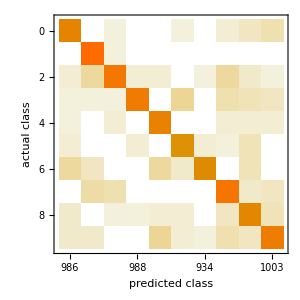

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

0.9816

```mathematica
{lossPlot,weightPlot,gradPlot}=NetTrain[lenet,trainingData,Automatic,{"LossEvolutionPlot","RMSWeightEvolutionPlot","RMSGradientEvolutionPlot"},MaxTrainingRounds->2,BatchSize->512,TargetDevice->"GPU"];
```

```mathematica
Column[{lossPlot,weightPlot,gradPlot}]
```

-Graphics-

### Exporting a trained net

```mathematica
Export["testnet.wlnet",trainedNet]
```

testnet.wlnet

```mathematica
trained=Import["testnet.wlnet"]
```

NetChain[<>]

```mathematica
cm=ClassifierMeasurements[trained,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.986

## Exercise

1. In this exercise we will classify a more complex  spiral system. 
a) In the first step you need to generate the spiral cluster. Use the following code to generate the cluster:
spiral[r_,p_]:=r{Sin[ 4r+p],Cos[4 r+p]}
makeCluster[class_,p_]:=spiral@@@RandomVariate[UniformDistribution[{{0,3},{p-0.5,p+0.5}}],1000]->class;
clusters=makeCluster@@@{{Red,0},{Green,4}};
Visualize the cluster differentiating the clusters by two different colors.
b) In the second step, create the training data and the NetChain. You will need two Fully Connected blocks with a non-linear classifying layer. 
c) Train the dataset with ADAM as method and a regularization of your choice.
d) Create the contour lines, by specifying the probability to 0.75. Visualize the results

Solution

## References and Glossary

Guide Page: guide/NeuralNetworks

Ian Goodfellow’s book: http://www.deeplearningbook.org/

STANFORD COURSES: 
Stanford CNN course: 
CS 231n: http://cs231n.stanford.edu/
https://www.youtube.com/playlist?list=PL3FW7Lu3i5JvHM8ljYj-zLfQRF3EO8sYv

Other Stanford courses that may be relevant: 
CS 224n: NLP with Deep Learning: http://cs224d.stanford.edu/
https://www.youtube.com/playlist?list=PL3FW7Lu3i5Jsnh1rnUwq_TcylNr7EkRe6

Good precursor for ML: http://cs229.stanford.edu/

COURSERA: 
1) Geoff Hinton’s Coursera course: https://www.coursera.org/learn/neural-networks

2) New course in coursera: https://www.coursera.org/specializations/deep-learning?utm_source=gg&utm_medium=sem&campaignid=904733485&adgroupid=45435009512&device=c&keyword=coursera%20deep%20learning&matchtype=e&network=g&devicemodel=&adpostion=1t1&creativeid=213802647355&hide_mobile_promo&gclid=EAIaIQobChMIj6bJ25f_1QIVFlgNCh0ejQ9FEAAYASAAEgJXGPD_BwE

AbsoluteTiming | AspectRatio | BatchNormalizationLayer | BatchSize | BinormalDistribution
CatenateLayer | ClassifierMeasurements | Classify | ColorSpace | ContourPlot
ContourStyle | Cos | CrossEntropyLossLayer | Darker | DeleteMissing
Dimensions | Dot | ElementwiseLayer | Epilog | ExampleData
Exp | False | Flatten | Frame | FrameLabel
FrameTicks | GrayLevel | Green | ImageDimension | Keys
List | ListLinePlot | ListPlot | LogisticSigmoid | MaxTrainingRounds
Mean | MeanAbsoluteLossLayer | MeanInputsPerSecond | MeanSquaredLossLayer | Method
N | NetChain | NetDecoder | NetEncoder | NetExtract
NetGraph | NetInitialize | NetPort | None | NormalDistribution
Plot | PlotLegends | PlotRange | PlotRangePadding | PlotStyle
Plus | Quantity | Quiet | RandomReal | RandomSample
RandomVariate | Range | Show | SoftmaxLayer | Table
TakeDrop | Tanh | Target | TargetDevice | Text
Thick | Thread | Times | Total | TotalLayer
TrainingProgressReporting | True | UniformDistribution | UnitVector |

## Improving Network Training: Methods

Vanilla Update 

•  Basic method (not in Wolfram Language) 
•  Update parameters in the negative direction of the gradient. 
•  Parameters x and the gradient dx, form used is: x→ x- lr ∂x

Momentum Update 

•  Basic method (not in Wolfram Language) 
•  Better convergence for rates on deep networks. 

• The update has the form: 
v = μ * v -lr *dx  # integrate velocity
x += v  # integrate position
Here we see an introduction of a variable, v, i.e. the velocity that is initialized at zero, and an additional hyperparameter μ, which is entered in the Wolfram Language (as Momentum) and related to viscosity in physical systems. 

Nesterov Momentum Update 

In this method of updating the momentum, we are looking one-step ahead, and as a result we have a little bit better guess for the step
(SGD in Wolfram Language)

v_prev = v # back this up
v = μ * v - lr * dx # velocity update stays the same
x += - μ * v_prev + (1 + μ) * v # position update changes form

-Graphics-
RMSProp
(RMSProp in Wolfram Language)

cache += Beta* cache + (1 - Beta) * dx**2
x += - Beta * dx / (Sqrt(cache) + ϵ)
Here, Beta is a hyperparameter and typical values are [0.9, 0.99, 0.999]. The smoothing term ϵ (~1e-4 to 1e-8) avoids division by zero. 

Geoff Hinton’s Coursera class http://www.cs.toronto.edu/~tijmen/csc321/slides/lecture_slides_lec6.pdf (Slide 29)

Adam
(Adam in Wolfram Language)
m = Beta1*m + (1-Beta1)*dx
v = Beta2*v + (1-Beta2)*(dx**2)
x += - lr * m / (Sqrt(v) + ϵ)

https://arxiv.org/pdf/1412.6980.pdf
Recommended values in the paper are ϵ = 1e-8, beta1 = 0.9, beta2 = 0.999.

## Improving Network Training: NetInitialize Methods

NetIntiailize[net] gives a net in which all uninitialized learnable parameters in net have been given initial values. By default, all methods initialize bias vectors to zero.

Most commonly used ones are:

Random : We want the weights to be very close to zero, but not identically zero. As a solution, it is common to initialize the weights of the neurons to small numbers and refer to doing so as symmetry breaking. The idea is that the neurons are all random and unique in the beginning, so they will compute distinct updates and integrate themselves as diverse parts of the full network. You can separately initialize the weight matrices and vectors using the suboptions present

W ∝ RandomVariate[NormalDistribution[0,0.1/0.01]]

Identity: One problem with the above suggestion is that the distribution of the outputs from a randomly initialized neuron has a variance that grows with the number of inputs. It turns out that we can normalize the variance of each neuron’s output to 1 by scaling its weight vector by the square root of the number of inputs. Initialize the net using the "Identity" method, which results in a net that attempts to preserve the components of tensors as they pass through linear layers

W ∝ RandomVariate[UniformDistribution[-1/√n_in,1/√n_in]]

Xavier

W ∝ RandomVariate[UniformDistribution[-r,r]]

http : // machinelearning.wustl.edu/mlpapers/paper_files/AISTATS2010_GlorotB10.pdf (Xavier et.al)

Tanh:  RandomVariate[UniformDistribution[-r,r]] ;  r =√(6/(n_in+n_out))

Sigmoid:  RandomVariate[UniformDistribution[-r,r]] ;  r =4 √(6/(n_in+n_out))

https://arxiv.org/pdf/1502.01852v1.pdf (He. et.al)

ReLU:  RandomVariate[UniformDistribution[-r,r]] ;  r =√(2/n_in)

Orthogonal: First initialize the weight matrix, then perform SingularValueDecomposition. W_init = RandomReal[{0,0.1}, {n,m}]; {W_fin,w,v} = SingularValueDecomposition[W_init ]; W_fin is your required weight

## Loss Layers

The LossLayers specifies the functional form of loss to be computed, which measures the compatibility between a prediction (e.g. the class scores in classification) and the actual value of the label. The data loss takes the form of an average over the data losses for every individual example. In the iteration of training the network, this explicit loss function is minimized by tuning the parameters (via back propagation).

### LossLayer types

Some of the implemented loss layers are follows:

MeanAbsoluteLossLayer : represents a loss layer that computes the mean absolute difference between the "Input" port and "Target" port. (Poisson type used for regression problem)

```mathematica
data=<|"Input"->{1,2,3},"Target"->{3,2,1}|>;
MeanAbsoluteLossLayer[][data]
meanAbsoluteLoss=N[Mean[Flatten[Abs[#Input-#Target]]]]&;
meanAbsoluteLoss[data]
```

1.33333

1.33333

MeanSquaredLossLayer : represents a loss layer that computes the mean squared difference between the "Input" port and "Target" port. (Gaussian type used for regression problem)

```mathematica
data=<|"Input"-> {1,2,3},"Target"->{3,2,1}|>;
MeanSquaredLossLayer[][data]
meanSquaredLoss=N[Mean[Flatten[(#Input-#Target)^2]]]&; 
meanSquaredLoss[data]//N
```

2.66667

2.66667

CrossEntropyLossLayer : represents a net layer that computes the information- theoretic distance by comparing probabilities with specified target values. (used for classification problem)

```mathematica
data=<|"Input"-> {0.1,0.2,0.7},"Target"->{0.12,0.3,0.6}|>;
CrossEntropyLossLayer["Probabilities"][data]
ceLoss=-Total[#Target*Log@#Input]&;
ceLoss[data]
```

0.973147

0.973147

ContrastiveLossLayer represents a loss layer that computes a loss based on a distance metric and a target that specifies whether the distance should be minimized or maximized.

```mathematica
loss=ContrastiveLossLayer[]
```

ContrastiveLossLayer[<>]

If the target is Truepaclet:ref/True, the loss is nonzero only when the input distance is less than the default margin of 0.5:

```mathematica
loss[<|"Input"->0.1,"Target"->True|>]
loss[<|"Input"->0.6,"Target"->True|>]
```

0.4

0.

If the target is Falsepaclet:ref/False, the loss is proportional to the input distance:

```mathematica
loss[<|"Input"->0.6,"Target"->False|>]
```

0.6

When a loss layer is chosen automatically for a port, the loss layer to use is based on the layer within the net whose output is connected to the port. For SoftmaxLayer and LogisticSigmoid, CrossEntropyLossLayer is chosen, for non-loss layers, MeanSquaredLossLayer is chosen. If a loss layer is specified, it is used unchanged. You can also make custom losses using the LossFunction.

## Training Optimization Layers

### Batch Normalization

BatchNormalizationwas developed by Ioffe and Szegedy (Feb 2015) to properly initialize neural networks by explicitly forcing the activations throughout a network to take on a unit gaussian distribution at the beginning of the training. A BatchNormalization layer is used immediately after fully connected layers (or convolutional layers), and before non-linearities. The parameters for the unit gaussian is learned from the MovingMean and MovingVariance, while the shift (“Beta”) and  scale parameters (“Gamma”) are trainable and can be learned from NetTrain.

-Graphics-

Source:https://arxiv.org/pdf/1502.03167.pdf

Dropout

Dropout is an extremely effective, simple regularization technique by Srivastava et al (June 2014). While training, dropout sets its input elements to zero with probability p, multiplying the remainder by 1/(1-p). By default, the value of p=0.5.

-Graphics-

Source:http://jmlr.org/papers/volume15/srivastava14a/srivastava14a.pdf

Local Response Normalization

Local Normalization helps in generalization. The LocalNormalizationLayer brings about “lateral inhibition” which is actually found in real neurons. The authors used the validation parameters

```mathematica
{{"Alpha", 10^-4, scaling parameter}, {"Beta", 0.75, power parameter}, {"Bias", 2.0, bias parameter}, {"ChannelWindowSize", 2, number of channels to average over}}
```

The output tensor O_ijk is obtained via O_ijk=T_ijk/D_ijk, where D_ijk=(α ∑_(x = max(1, i-c))^(min(N, c+i)) T_xjk^2+b)^β, T_ijk is the input, α is the "Alpha" parameter, β is the "Beta" parameter, c is the "ChannelWindowSize" and N is the number of channels in the input T_ijk.

http://www.cs.toronto.edu/~fritz/absps/imagenet.pdf

Instance Normalization:

InstanceNormalization by Ulyanov et al. (Jul 2016) prevents instance-specific mean and covariance shift simplifying the learning process. The authors show in the paper that InstanceNormalization dramatically improve the performance of certain deep neural networks for image generation.

Consider an input tensor I_cs, where c is the channel dimension and s represents all the spatial dimensions flattened together. Then the output O_cs is obtained via O_cs=γ_c(I_cs-μ_c)/√(σ_c^2-ϵ)+β_c, where the mean is given by μ_c=∑_(s=1)^S I_cs/S, the variance by σ_c^2=∑_(s=1)^S (I_cs-μ_c)^2/S, β_c is the "Beta" parameter, γ_c is the "Gamma" parameter, and S is the total size of the spatial s dimension.

https://arxiv.org/pdf/1607.08022.pdf

Layer Normalization:

They computed the mean and variance used for normalization from all of the summed inputs to the neurons in a layer on a single training case. Like batch normalization, each neuron has its own adaptive bias and gain applied after the normalization but before the non-linearity. Unlike batch normalization, layer normalization performs exactly the same computation at training and test times (and applicable to recurrent nets)